#### 2.2.2 Logistic Equation with Periodic Injection

```mathematica
Quit[];
```

```mathematica
$Assumptions = β>0 && k>0 &&d>0 && t≳ 0 ;
```

```mathematica
f[t_]:=Piecewise[{{1,t<1},{Exp[-d],1<t<2},{Exp[-2*d],2<t<3},{Exp[-3*d],3<t<4},{Exp[-4*d],4<t<5},{Exp[-5*d],t>5}}]
```

```mathematica
q[t_]:=q0*k*Exp[β*t]*f[t]/(k+q0*Integrate[β*Exp[β*T]*f[T],{T,0,t},Assumptions->Element[t,Reals]])
```

Computing limits and finding the size of the relative jumps to ensure the vasculature is being killed in the same ratio.

```mathematica
Limit[q[t],t->0]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

q0

```mathematica
Limit[q[t],t->Infinity]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

k

```mathematica
l11=Limit[q[t],t->1,Direction->"FromBelow"]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

(ⅇ^β k q0)/(k+(-1+ⅇ^β) q0)

```mathematica
l12=Limit[q[t],t->1,Direction->"FromAbove"]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

(ⅇ^(-d+β) k q0)/(k+(-1+ⅇ^β) q0)

```mathematica
j1=Simplify[(l11-l12)/l11]
```

1-ⅇ^-d

```mathematica
q0=3;k=30;β=0.75;d=0.50;
```

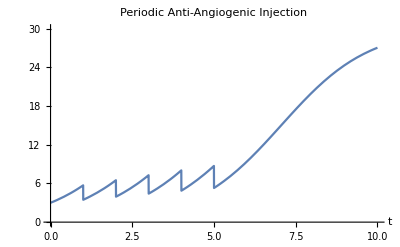

```mathematica
Plot[q[t],{t,0,10},PlotRange->{0,30},ExclusionsStyle->Dashed,AxesLabel->Automatic,PlotLabel->"Periodic Anti-Angiogenic Injection"]
```